```mathematica
fontName="Times";
SetOptions[Plot,FrameStyle->Directive[Thickness[0.002],13,fontName],GridLines->Automatic,GridLinesStyle->Directive[Thickness[0.001],Black],LabelStyle->(FontFamily->fontName),ImageSize->300,Frame->True,PlotStyle->Thick];
```

```mathematica
A={0,-d};L2={l Cos[θ[t]],l Sin[θ[t]]};L1=-L2;
Subscript[R, a]=L1-A;Subscript[R, b]=-A;Subscript[R, c]=L2-A;
Subscript[r, a]=(Subscript[R, a].Subscript[R, a])^(1/2);Subscript[r, b]=(Subscript[R, b].Subscript[R, b])^(1/2);Subscript[r, c]=(Subscript[R, c].Subscript[R, c])^(1/2);
```

```mathematica
Subscript[r, ba]=({{Cos[θ[t]], -Sin[θ[t]]}, {Sin[θ[t]], Cos[θ[t]]}}).({-l,0 });
Subscript[r, bb]={0,0};
Subscript[r, bc]=({{Cos[θ[t]], -Sin[θ[t]]}, {Sin[θ[t]], Cos[θ[t]]}}).({l,0 });
Cm=Subscript[k, c]({{1/R1, 1/Subscript[r, a], 1/Subscript[r, b], 1/Subscript[r, c]}, {1/Subscript[r, a], 1/R2a, 1/l, 1/2l}, {1/Subscript[r, b], 1/l, 1/R2b, 1/l}, {1/Subscript[r, c], 1/2l, 1/l, 1/R2c}});
Cm1=Inverse[Cm]//Simplify;
({{q10}, {q2a}, {q2b}, {q2c}})=Cm1.({{-Φ}, {Φ}, {Φ}, {Φ}});
```

```mathematica
Subscript[F, 2a]=-(Subscript[k, c] q10 q2a)/Subscript[r, a]^3 Subscript[R, a];
Subscript[F, 2b]=-(Subscript[k, c] q10 q2b)/Subscript[r, b]^3 Subscript[R, b];
Subscript[F, 2c]=-(Subscript[k, c] q10 q2c)/Subscript[r, c]^3 Subscript[R, c];
Qa[t_]:=-Subscript[k, c]q2a q10;
Qc[t_]:=-Subscript[k, c]q2c q10;
```

```mathematica
ET=(J θ'[t]^2)/2
```

1/2 J θ'[t]^2

```mathematica
Q1=D[Subscript[r, ba],θ[t]].Subscript[F, 2a]+D[Subscript[r, bc],θ[t]].Subscript[F, 2c]
```

(l^2 Cos[θ[t]] 3 k_c)/((l^2 Cos[θ[t]]^2+(d-l Sin[θ[t]])^2)^(3/2))+(l Cos[θ[t]] (d-1) 1 ((2 Φ ((1-2/1)/R1+2/1-l/1-2/1+2/(d^2 l+l^3+1)))/((-l^2/(R1 R2b)+(l^2-1)/d^2+10+(4 1)/l^2+(4/R1+1)/l) k_c)+1/1-1+1) k_c)/((l^2 Cos[θ[t]]^2+(d-l Sin[θ[t]])^2)^(3/2))+(l^2 Cos[θ[t]] 3 k_c)/((l^2 1^2+1^2)^(3/2))-(l Cos[θ[t]] 3 k_c)/((l^2 Cos[θ[t]]^2+(d+l Sin[θ[t]])^2)^(3/2))
 |  |  |  |

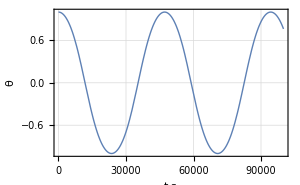

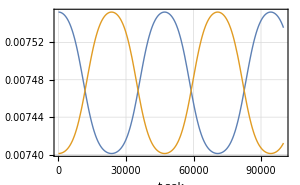

```mathematica
params={Φ->20000,Subscript[k, c]->8.99 10^9,R2a->.59,R2c->.59,R2b->.65,R1->.5,l->1.5,d->15,J->1000};
tk=100000;
eq = D[D[ET, D[θ[t],t]],t]-D[ET,θ[t]]==Q1//.params;
sol = NDSolve[{eq,θ[0]==1.,θ'[0]==0.},θ[t],{t,0,tk}];
Plot[{θ[t]}/.sol//Evaluate,{t,0,tk},AxesLabel->{"t,s","θ"},PlotRange->All]
Plot[{Qa[t]//.params,Qc[t]//.params}/.sol//Evaluate,{t,0,tk},AxesLabel->{"t,sek","θ"},PlotRange->All]
```

```mathematica
}
```